```mathematica
f[x_]:=NestWhile[#/2&,x,EvenQ]
Collatz[a0_Integer,maxits_:1000]:=NestWhileList[If[EvenQ[#],#/2,3#+1]&,a0,Unequal[#,1,-1,-10,-34]&,1,maxits]

Terras[a0_Integer,maxits_:1000]:=NestWhileList[If[EvenQ[#],#/2,(3#+1)/2]&,a0,Unequal[#,1,-1,-10,-34]&,1,maxits]
```

```mathematica
nCollatz[a0_Integer,maxits_:1000]:=NestWhileList[If[EvenQ[#],f[#],f[(3#+1)]]&,a0,Unequal[#,1,-1,-10,-34]&,1,maxits]
```

```mathematica
g[x_]:=Flatten[Collatz[x]]
```

```mathematica
Partition[Collatz[1000],3]
```

```mathematica
d[x_]:=Table[1,{i,1,x}]
Manipulate[Graphics[Arrow[Partition[Collatz[n],2]]],{n,3,1000,1}]
```

```mathematica
Manipulate[Graphics[Arrow[Partition[Flatten[Map[g,Table [n,{n,2,m}]]],2]]],{m,1,1000,1}]
```

```mathematica
VertexList[%12]
```

```mathematica
ArrayPlot/@ Map[d,Table[Collatz[n],{n,12,20}],{2}]//TableForm
```

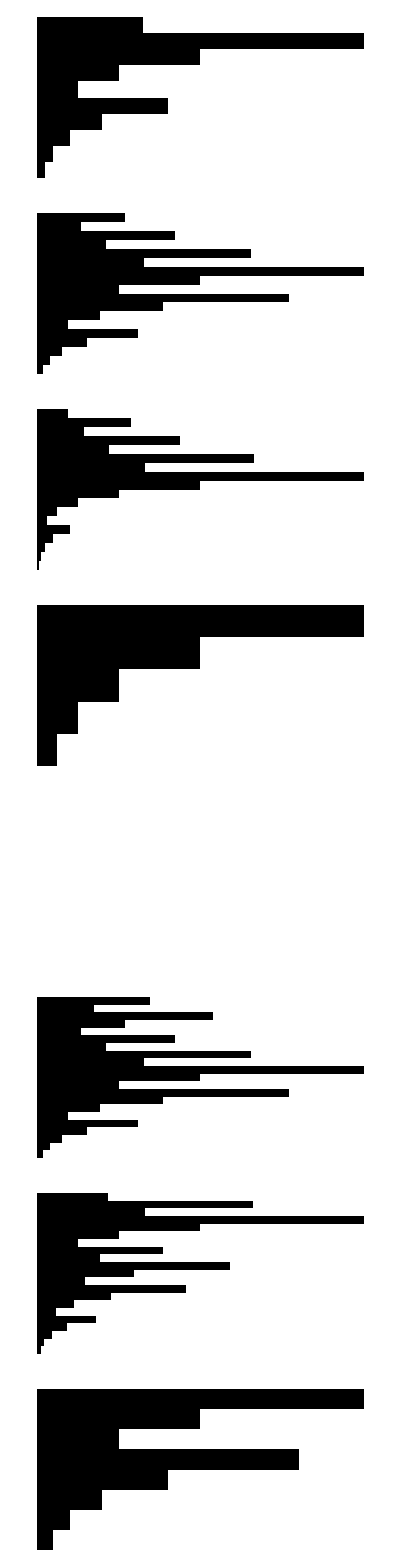

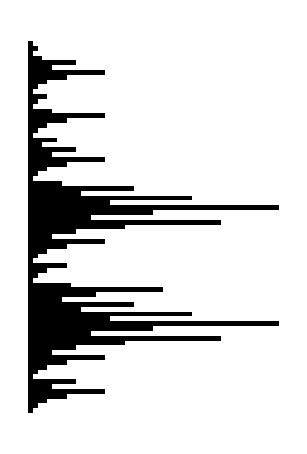

```mathematica
ArrayPlot[Flatten[Map[d,Table[Collatz[n],{n,1,100}],{2}],1]]
```

```mathematica
Manipulate[ListPlot[Flatten[Table[Collatz[n],{n,a,b}]]],{a,1,1000,1},{b,1,1000,1}]
```

```mathematica
~
```